## Setup

```mathematica
Clear["Global`*"]
SetDirectory@NotebookDirectory[];
BigFractionStyle=Style[#,DefaultOptions->{FractionBoxOptions->{AllowScriptLevelChange->False}}]&;
```

```mathematica
<<MaTeX`
TeX=MaTeX[#,FontSize->14,"Preamble"-> {"\\usepackage{mathpazo}"}]&;
```

## Metric

```mathematica
𝒞={t,r,θ,ϕ};
𝒟=Length[𝒞];
Δ[r_]=r^2-2 M r+a^2;
Σ[r_,θ_]=r^2+a^2 Cos[θ]^2;
g={{-(Δ[r]-a^2 Sin[θ]^2)/Σ[r,θ],0,0,-a Sin[θ]^2(r^2+a^2-Δ[r])/Σ[r,θ]},{0,Σ[r,θ]/Δ[r],0,0},{0,0,Σ[r,θ],0},{-a Sin[θ]^2(r^2+a^2-Δ[r])/Σ[r,θ],0,0,(((r^2+a^2)^2-Δ[r] a^2 Sin[θ]^2) Sin[θ]^2)/Σ[r,θ]}};
Ig=Inverse[g]//FullSimplify;
VolG=PowerExpand@Simplify@Sqrt[-Det@g]
g//MatrixForm//BigFractionStyle
```

1/2 (a^2+2 r^2+a^2 Cos[2 θ]) Sin[θ]

(-(a^2-2 M r+r^2-a^2 Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | -(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
0 | (r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
-(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | (Sin[θ]^2 ((a^2+r^2)^2-a^2 (a^2-2 M r+r^2) Sin[θ]^2))/(r^2+a^2 Cos[θ]^2))

```mathematica
gK={{-(Δ[r]-a^2 Sin[θ]^2)/Σ[r,θ],1,0,-a Sin[θ]^2(r^2+a^2-Δ[r])/Σ[r,θ]},{1,0,0,-a Sin[θ]^2},
{0,0,Σ[r,θ],0},
{-a Sin[θ]^2(r^2+a^2-Δ[r])/Σ[r,θ],-a Sin[θ]^2,0,(((r^2+a^2)^2-Δ[r] a^2 Sin[θ]^2) Sin[θ]^2)/Σ[r,θ]}};
IgK=Inverse[gK]//FullSimplify;
VolGK=PowerExpand@Simplify@Sqrt[-Det@gK];
gK//MatrixForm//BigFractionStyle
```

(-(a^2-2 M r+r^2-a^2 Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 1 | 0 | -(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
1 | 0 | 0 | -a Sin[θ]^2
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
-(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | -a Sin[θ]^2 | 0 | (Sin[θ]^2 ((a^2+r^2)^2-a^2 (a^2-2 M r+r^2) Sin[θ]^2))/(r^2+a^2 Cos[θ]^2))

## Christoffel, Riemann, Ricci

```mathematica
Clear[δg,Γ,Riemann,Ricci,R,Einstein]
δg=D[g, {𝒞}];
Γ=Simplify[1/2 TensorContract[Ig⊗(TensorTranspose[δg,{1,2,3}]+TensorTranspose[δg,{1,3,2}]-TensorTranspose[δg,{2,3,1}]),{{2,3}}]];
Riemann=ParallelTable[Simplify[D[Γ⟦ρ,ν,σ⟧, 𝒞⟦μ⟧]-D[Γ⟦ρ,μ,σ⟧, 𝒞⟦ν⟧]+∑_(λ=1)^𝒟 (Γ⟦ρ,μ,λ⟧ Γ⟦λ,ν,σ⟧-Γ⟦ρ,ν,λ⟧ Γ⟦λ,μ,σ⟧)],{ρ,𝒟},{σ,𝒟},{μ,𝒟},{ν,𝒟}];
Ricci=Simplify[TensorContract[Riemann,{{1,3}}]];
R=Simplify[TensorContract[Ig⊗Ricci,{{1,3},{2,4}}]];
Einstein=Simplify[Ricci-(R g)/2];
```

```mathematica
intRules={M->Im@ZetaZero[2],a->Im@ZetaZero[1],r->Im@ZetaZero[3]};
solM=-1/(8Pi)VolGK/2(ParallelSum[dx[i]·dx[j]LeviCivitaTensor[4]⟦α,β,i,j⟧ D[gK⟦1,ν⟧, 𝒞⟦μ⟧] IgK⟦α,μ⟧ IgK⟦β,ν⟧,{α,𝒟},{β,𝒟},{ν,𝒟},{μ,𝒟},{i,𝒟},{j,𝒟}]/.{dx[i_]·dx[j_]:>-(dx[j]·dx[i])/;OrderedQ[{j,i}]})//.{x_·y_->x y,dx[1]->0 dx[4],dx[2]->0,dx[3]->1,dx[4]->1}//Simplify
```

-(M (a^2+r^2) (a^2-2 r^2+a^2 Cos[2 θ]) Sin[θ])/(2 π (a^2+2 r^2+a^2 Cos[2 θ])^2)

```mathematica
solJ=1/(16Pi)VolGK/2(ParallelSum[dx[i]·dx[j]LeviCivitaTensor[4]⟦i,j,α,β⟧IgK⟦α,μ⟧ IgK⟦β,ν⟧D[gK⟦4,ν⟧, 𝒞⟦μ⟧] ,{α,𝒟},{β,𝒟},{ν,𝒟},{μ,𝒟},{i,𝒟},{j,𝒟}]//.{dx[i_]·dx[j_]:>-(dx[j]·dx[i])/;OrderedQ[{j,i}]})//.{x_·y_->x y,dx[1]->0 g[[1,4]]/g[[1,1]]dx[4],dx[2]->0,dx[3]->1,dx[4]->1}//Simplify
```

-(a M (a^4-3 a^2 r^2-6 r^4+a^2 (a^2-r^2) Cos[2 θ]) Sin[θ]^3)/(4 π (a^2+2 r^2+a^2 Cos[2 θ])^2)

```mathematica
solJ//Limit[#,r->∞]&//2Pi Integrate[#,{θ,0,Pi}]&
```

a M

## Metric Functions

```mathematica
Clear[RaiseInd,LowerInd,ChangeInd]
RaiseInd[T_List,i:{__Integer}|_Integer]:=Fold[
TensorContract[
TensorTranspose[#1⊗Ig,Cycles[{{#2,TensorRank@T+2}}]],
{TensorRank@T+{1,2}}
]&,T,Flatten@{i}]
LowerInd[T_List,i:{__Integer}|_Integer]:=Fold[
TensorContract[
TensorTranspose[#1⊗g,Cycles[{{#2,TensorRank@T+2}}]],
{TensorRank@T+{1,2}}
]&,T,Flatten@{i}]
ChangeInd[T_,{u:{___Integer},d:{___Integer}}]:=LowerInd[RaiseInd[T,u],d];
```

## Calculations

```mathematica
Ricci//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Rie2=Simplify@TensorContract[Riemann⊗ChangeInd[Riemann,{{2,3,4},{1}}],{Range[1,4],Range[5,8]}ᵀ];
```

```mathematica
Rie2==(48 M^2(r^2-a^2 Cos[θ]^2)((r^2+a^2 Cos[θ]^2)^2-16 r^2 a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^6)//Simplify
```

True

```mathematica
Limit[Rie2,{r-> 0,θ->Pi/2}]//Simplify
```

{-(48 M^2 Sec[θ]^6)/a^6,(48 M^2)/r^6}

## Kerr-Child plot

```mathematica
Clear@PlotKG;
vp={6.73,3.828,0.975};
PlotKG[rd_,color_,op_:0.2,lg_:None]:=ContourPlot3D[(r^4-r^2 (x^2+z^2+y^2-a^2)-a^2 z^2==0)/.{a->1,r->rd} //Evaluate,{x,-2,2},{y,-2,2},{z,-2,2},RegionFunction->Function[{x,y,z},Abs[ArcTan[x,y]-Pi/4]≥Pi/4Boole[rd>0.1]],ContourStyle->Directive[Opacity[op],color],PlotPoints->60,Mesh->None,PlotLegends->lg,BoundaryStyle->Darker@color]
p1=Show[PlotKG[1.5,Red,0.2],PlotKG[1,Green,0.3],PlotKG[0.6,Blue,0.35],PlotKG[0.001,Gray,1],Graphics3D[{AbsoluteThickness[1.2],Arrow[{{0,0,0},2.0 #}]&/@IdentityMatrix[3]}],ViewPoint->vp,Boxed-> False,BoxRatios->1,Axes->False,PlotRangePadding->0];
Show[p1,Method->{"ShrinkWrap"->True}]
Export["Thesis/Figures/kerrchild3d.pdf",p1]
```

-Graphics3D-

Thesis/Figures/kerrchild3d.pdf

```mathematica
f2=Append[Flatten@Table[{Callout[Sqrt[(r^4-r^2 (x^2-a^2))/(a^2+r^2)],TeX@ToString[r,InputForm],0.1+0.3r,0.3r,CalloutStyle->Black],-Sqrt[(r^4-r^2 (x^2-a^2))/(a^2+r^2)]},{r,{1/2,1,3/2}}],Callout[If[x^2≤1,0,Undefined],TeX@0,0.2,0.1,CalloutStyle->Black]]/.a->1;
c2=Append[Flatten[{#,#}&/@Reverse@{Red,Darker@Green,Darker@Blue}],Black];
p2=Plot[f2//Evaluate,{x,-2,2.2},PlotStyle->c2,Axes->True,Frame->None,AxesStyle->Arrowheads[{0,0.04}],PlotRange->{{-2.3,2.3},{-2.2,2.4}},AspectRatio->1,Ticks->{Table[{x,TeX[x],{0.015,0.015}},{x,{-2,-1,1,2}}]},Epilog->{Text[TeX[z/a],{0.2,2.2}],Text[TeX[x/a],{2.2,0.35}]}
];
θ2=Table[((x^2 Cos[θ] Cot[θ])/(z^2+a^2 Cos[θ]^2)==Sin[θ])/.{a->1},{θ,{0.05Pi,0.15Pi,0.25Pi,0.4Pi}}];
p3=ContourPlot[θ2//Evaluate,{x,-2.3,2.3},{z,-2.2,2.4},ContourStyle->{{Dashed,Thin,Gray,Opacity[0.65]}},RegionFunction->Function[{x,z},r^4-r^2(x^2-1)>z^2(1+r^2)/.r->1.6],
Frame->None];
Export["Thesis/Figures/kerrchild2d.pdf",Echo@Show[p2,p3]]
```

-Graphics-

Thesis/Figures/kerrchild2d.pdf

## Geodesics

```mathematica
NullGeodesic[a0_,e0_,l0_]:=Module[{U={t[τ],r[τ],0,ϕ[τ]},gU=g/.{r->r[τ],t->t[τ],ϕ->ϕ[τ]},param,eq,ics,T,TMAX,TSOL},
param={δ->1,ϵ->e0,ℓ->l0,a->a0,θ->π/2,M->1};
eq={{1,0,0,0}.gU.D[U, τ]==-ϵ,{0,0,0,1}.gU.D[U, τ]==ℓ,(D[U, τ]).gU.(D[U, τ])==δ};
ics={t[0]==0,r[0]==20,ϕ[0]==0};
T=50;
sol=Quiet@First@NDSolve[Flatten[{eq,ics}]/.param,{t,r,ϕ},{τ,0,T}];
TMAX=sol[[1,2,1,1,2]];
TSOL=τ/.Quiet@FindRoot[(r[τ]-1-Sqrt[1-a0^2])/.sol,{τ,0.5 TMAX},AccuracyGoal->10,PrecisionGoal->15];
ParametricPlot[r[τ]{Cos[ϕ[τ]],Sin[ϕ[τ]]}/.sol//Evaluate,{τ,0,Min[T,TMAX,0.998TSOL]},PlotRange->{{-5,20},{-5,5}},Axes->False,Epilog->{{Dotted,Circle[{0,0},2]},Thick,Circle[{0,0},1+Sqrt[1-a0^2]],Text[TeX["\\textbf{BH}"],{0,0}]}]]
```

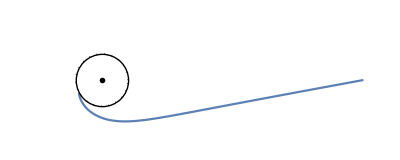

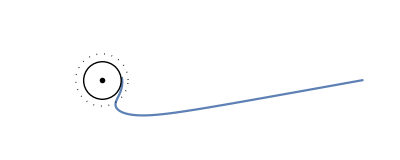

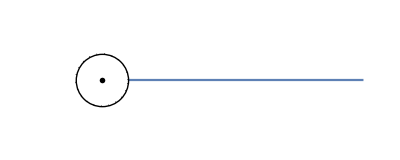

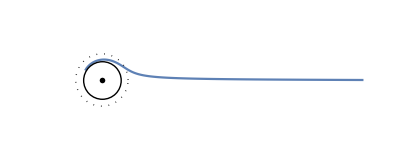

{Thesis/Figures/geodKerr_0_-5.pdf,Thesis/Figures/geodKerr_90_-5.pdf,Thesis/Figures/geodKerr_0_0.pdf,Thesis/Figures/geodKerr_90_0.pdf}

```mathematica
Export[StringRiffle[{"Thesis/Figures/geodKerr",Round[100#1,1],#2},"_"]<>".pdf",Echo@Show[NullGeodesic[#1,1,#2],Method->{"ShrinkWrap"-> True}]]&@@@{{0,-5},{0.9,-5},{0,0},{0.9,0}}
```

## Ergoregion

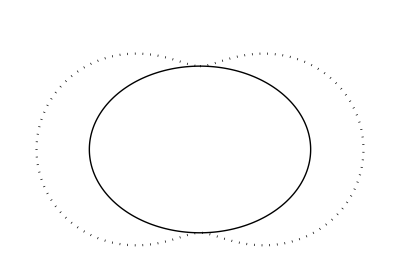

```mathematica
g1=ParametricPlot[{Sqrt[r^2+a^2]Sin[θ],r Cos[θ]}/.{{r->1+Sqrt[1-a^2]},{r->1+Sqrt[1-a^2 Cos[θ]^2]}}/.a->0.99//Evaluate,{θ,0,2Pi},PlotStyle->{{Black,Thick},{Black,Dotted}}//Evaluate,Axes->False,Ticks->None,PlotRange->{Automatic,{-1.4,1.7}}]
```

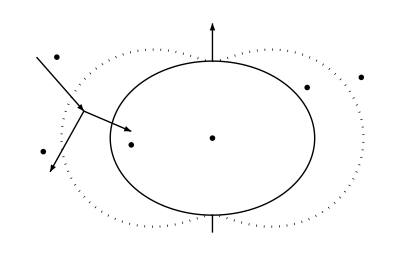

Thesis/Figures/ergoPenrose.pdf

```mathematica
P0={-1.9,0.4};
g2=Show[Graphics[{
Arrowheads[0.02],
Arrow[{{-2.6,1.2},P0}],
Arrow[{P0,{-2.4,-0.5}}],
Arrow[{P0,{-1.2,0.1}}],
Text[TeX["\\mathbf{BH}"],{0,0}],
Text[TeX["r_+"],{1.4,0.75}],
Text[TeX["r_\\mathrm{ergo}"],{2.2,0.9}],
Arrowheads[0.05],
Arrow[{{0,1+Sqrt[1-0.99^2]},{0,1.7}}],
Line[{-{0,1+Sqrt[1-0.99^2]},{0,-1.4}}],
Text[TeX["p"],{-2.3,1.2}],
Text[TeX["p_1"],{-1.2,-0.1}],
Text[TeX["p_2"],{-2.5,-0.2}]
}],g1];
Export["Thesis/Figures/ergoPenrose.pdf",Echo@g2]
```